# Hubbard Dimer NSSR

## Variables to be set

Set number of fermionic modes, .i.e: number of sites * 2for spins

```mathematica
nsites = 2;
numModes=nsites*2;
```

## General definitions - Jordan Wigner Transformation

Creation, annihilation operator and vacuum

```mathematica
c={{0,1},{0,0}};
a={{0,0},{1,0}};
```

```mathematica
vac={{0},{1}};
```

Pauli Matrices

```mathematica
s0=IdentityMatrix[2];
sz={{1,0},{0,-1}};
```

Extension to all modes

```mathematica
Ops[pos_,op_]:=KroneckerProduct@@Table[Which[k<pos,sz,k==pos,op,True,s0],{k,1,numModes}];
upMode[i_]:=2 i-1;
dnMode[i_]:=2 i;

cu[i_]:=Ops[upMode[i],c];
cd[i_]:=Ops[dnMode[i],c];
au[i_]:=Ops[upMode[i],a];
ad[i_]:=Ops[dnMode[i],a];

nu[i_]:= cu[i].au[i];
nd[i_]:= cd[i].ad[i];
```

```mathematica
vacuumFull=Fold[KroneckerProduct,vac,Table[vac,{numModes-1}]];
```

Spin Operators

```mathematica
Sp[i_]:=cu[i].ad[i];
Sm[i_]:=cd[i].au[i];
Sz[i_]:=1/2 (nu[i]-nd[i]);
```

summed spins

```mathematica
SpTot=Sum[Sp[i],{i,1,nsites}];
SmTot=Sum[Sm[i],{i,1,nsites}];
SzTot=Sum[Sz[i],{i,1,nsites}];
```

S.b2

```mathematica
S2=SzTot.SzTot+1/2 (SpTot.SmTot+SmTot.SpTot);
```

Hoppings in Hamiltonian and edges also feature reversed as for tight binding model

```mathematica
neighbors=Table[{i,1+Mod[i,nsites]},{i,1,nsites}];
(* edges=Join[neighbors,neighbors/.{i_,j_}:>{j,i}] *)
edges = neighbors
```

{{1,2},{2,1}}

Hubbard Hamiltonian

```mathematica
t = t
U = U
```

t

U

```mathematica
H=-t * Sum[Module[{ii=pair[[1]],jj=pair[[2]]},cu[ii].au[jj]+cd[ii].ad[jj]],{pair,edges}] + U*Sum[nu[i].nd[i],{i,1,nsites}]-(mu)*Sum[nu[i]+nd[i],{i,1,nsites}];
```

```mathematica
{vals1,vecs1}=Eigensystem[H];
normeigvecs1=Normalize/@vecs1;
V1=Transpose[vecs1];
HD1=DiagonalMatrix[vals1];
```

```mathematica
rhoSolution=V1.DiagonalMatrix[Exp[-β * vals1]].Inverse[V1]; (*/Tr[DiagonalMatrix[Exp[-β * vals1]]]*)
H/.t->1/.U->2//MatrixForm
```

(4-4 mu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2-3 mu | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2-3 mu | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2-2 mu | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 2-3 mu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 mu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -2 mu | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -mu | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2-3 mu | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 mu | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 mu | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -mu | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 2-2 mu | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -mu | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -mu | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Two-Site Reduced Density Matrix

```mathematica
ident=KroneckerProduct@@Table[s0,{k,1,numModes}];
```

diagonal elements

```mathematica
A0101[i_,j_]:=(ident-nu[i]).(ident-nd[i]).(ident-nu[j]).(ident-nd[j]);

A0202[i_,j_]:=(ident-nu[i]).(ident-nd[i]).(ident-nu[j]).nd[j];
A0303[i_,j_]:=(ident-nu[i]).(ident-nd[i]).nu[j].(ident-nd[j]);
A0404[i_,j_]:=(ident-nu[i]).nd[i].(ident-nu[j]).(ident-nd[j]);
A0505[i_,j_]:=nu[i].(ident-nd[i]).(ident-nu[j]).(ident-nd[j]);

A0606[i_,j_]:=(ident-nu[i]).(ident-nd[i]).nu[j].nd[j];
A0707[i_,j_]:=(ident-nu[i]).nd[i].(ident-nu[j]).nd[j];
A0808[i_,j_]:=nu[i].(ident-nd[i]).(ident-nu[j]).nd[j];
A0909[i_,j_]:=(ident-nu[i]).nd[i].nu[j].(ident-nd[j]);
A1010[i_,j_]:=nu[i].(ident-nd[i]).nu[j].(ident-nd[j]);
A1111[i_,j_]:= nu[i].nd[i].(ident-nu[j]).(ident-nd[j]);

A1212[i_,j_]:= (ident-nu[i]).nd[i].nu[j].nd[j];
A1313[i_,j_]:= nu[i].(ident-nd[i]).nu[j].nd[j];
A1414[i_,j_]:= nu[i].nd[i].(ident-nu[j]).nd[j];
A1515[i_,j_]:= nu[i].nd[i].nu[j].(ident-nd[j]);

A1616[i_,j_]:= nu[i].nd[i].nu[j].nd[j];
```

non-diagonal elements

```mathematica
A0204[i_,j_]:=1/2(cd[i].ad[j]+cd[j].ad[i]).(ident-nu[i]).(ident-nu[j]);
A0305[i_,j_]:=1/2(cu[i].au[j]+cu[j].au[i]).(ident-nd[i]).(ident-nd[j]);

A0806[i_,j_]:=1/2(cu[i].au[j]+cu[j].au[i]).(ident-nd[i]).nd[j]; 
A0906[i_,j_]:=-1/2(cd[i].ad[j]+cd[j].ad[i]).(ident-nu[i]).nu[j];

A1106[i_,j_]:=1/2(cu[i].cd[i].ad[j].au[j]+cu[j].cd[j].ad[i].au[i]);
A0809[i_,j_]:=1/2(cu[j].cd[i].au[i].ad[j]+cd[j].cu[i].ad[i].au[j]);
A0811[i_,j_]:=1/2(cd[j].ad[i]+cd[i].ad[j]).nu[i].(ident-nu[j]);
A0911[i_,j_]:=-1/2(cu[j].au[i]+cu[i].au[j]).nd[i].(ident-nd[j]);

A1214[i_,j_]:=-1/2(cu[j].au[i]+cu[i].au[j]).nd[i].nd[j];
A1315[i_,j_]:=-1/2(cd[j].ad[i]+cd[i].ad[j]).nu[i].nu[j];

rhoMatrix[i_,j_,rhoSolution_,Z_]:=Module[{rho=ConstantArray[0,{16,16}]},(*Diagonal elements*)
rho[[1,1]]=Tr[A0101[i,j].rhoSolution]/Z;
rho[[2,2]]=Tr[A0202[i,j].rhoSolution]/Z;
rho[[3,3]]=Tr[A0303[i,j].rhoSolution]/Z;
rho[[4,4]]=Tr[A0404[i,j].rhoSolution]/Z;
rho[[5,5]]=Tr[A0505[i,j].rhoSolution]/Z;
rho[[6,6]]=Tr[A0606[i,j].rhoSolution]/Z;
rho[[7,7]]=Tr[A0707[i,j].rhoSolution]/Z;
rho[[8,8]]=Tr[A0808[i,j].rhoSolution]/Z;
rho[[9,9]]=Tr[A0909[i,j].rhoSolution]/Z;
rho[[10,10]]=Tr[A1010[i,j].rhoSolution]/Z;
rho[[11,11]]=Tr[A1111[i,j].rhoSolution]/Z;
rho[[12,12]]=Tr[A1212[i,j].rhoSolution]/Z;
rho[[13,13]]=Tr[A1313[i,j].rhoSolution]/Z;
rho[[14,14]]=Tr[A1414[i,j].rhoSolution]/Z;
rho[[15,15]]=Tr[A1515[i,j].rhoSolution]/Z;
rho[[16,16]]=Tr[A1616[i,j].rhoSolution]/Z;
(*Selected off-diagonal elements*)
rho[[2,4]]=rho[[4,2]]=Tr[A0204[i,j].rhoSolution]/Z;
rho[[3,5]]=rho[[5,3]]=Tr[A0305[i,j].rhoSolution]/Z;
rho[[8,6]]=rho[[6,8]]=Tr[A0806[i,j].rhoSolution]/Z;
rho[[9,6]]=rho[[6,9]]=Tr[A0906[i,j].rhoSolution]/Z;
rho[[11,6]]=rho[[6,11]]=Tr[A1106[i,j].rhoSolution]/Z;
rho[[8,9]]=rho[[9,8]]=Tr[A0809[i,j].rhoSolution]/Z;
rho[[8,11]]=rho[[11,8]]=Tr[A0811[i,j].rhoSolution]/Z;
rho[[9,11]]=rho[[11,9]]=Tr[A0911[i,j].rhoSolution]/Z;
rho[[12,14]]=rho[[14,12]]=Tr[A1214[i,j].rhoSolution]/Z;
rho[[13,15]]=rho[[15,13]]=Tr[A1315[i,j].rhoSolution]/Z;
(*Return the computed 16x16 matrix*)rho]
```

```mathematica
getRhoFTB[i_,j_]:=Module[{rhoAB,rhoABTb},rhoAB=rhoMatrix[i,j,rhoSolution,Tr[rhoSolution]];(*your 16x16 density matrix*)rhoABTb=ConstantArray[0,{16,16}];
rhoABTb[[1,1]]=rhoAB[[1,1]];
rhoABTb[[1,7]]=I*rhoAB[[2,4]];
rhoABTb[[1,10]]=I*rhoAB[[3,5]];
rhoABTb[[1,11]]=rhoAB[[11,6]];
rhoABTb[[2,2]]=rhoAB[[2,2]];
rhoABTb[[2,13]]=I*rhoAB[[8,6]];
rhoABTb[[3,3]]=rhoAB[[3,3]];
rhoABTb[[3,12]]=I*rhoAB[[9,6]];
rhoABTb[[4,4]]=rhoAB[[4,4]];
rhoABTb[[4,15]]=I*rhoAB[[9,11]];
rhoABTb[[5,5]]=rhoAB[[5,5]];
rhoABTb[[5,14]]=I*rhoAB[[8,11]];
rhoABTb[[6,6]]=rhoAB[[6,6]];
rhoABTb[[7,1]]=I*rhoAB[[2,4]];
rhoABTb[[7,7]]=rhoAB[[7,7]];
rhoABTb[[7,10]]=rhoAB[[8,9]];
rhoABTb[[7,16]]=I*rhoAB[[12,14]];
rhoABTb[[8,8]]=rhoAB[[8,8]];
rhoABTb[[9,9]]=rhoAB[[9,9]];
rhoABTb[[10,1]]=I*rhoAB[[3,5]];
rhoABTb[[10,7]]=rhoAB[[8,9]];
rhoABTb[[10,10]]=rhoAB[[10,10]];
rhoABTb[[10,16]]=I*rhoAB[[13,15]];
rhoABTb[[11,11]]=rhoAB[[11,11]];
rhoABTb[[12,3]]=I*rhoAB[[9,6]];
rhoABTb[[12,12]]=rhoAB[[12,12]];
rhoABTb[[13,2]]=I*rhoAB[[8,6]];
rhoABTb[[13,13]]=rhoAB[[13,13]];
rhoABTb[[14,5]]=I*rhoAB[[8,11]];
rhoABTb[[14,14]]=rhoAB[[14,14]];
rhoABTb[[15,4]]=I*rhoAB[[9,11]];
rhoABTb[[15,15]]=rhoAB[[15,15]];
rhoABTb[[16,6]]=rhoAB[[11,6]];
rhoABTb[[16,7]]=I*rhoAB[[12,14]];
rhoABTb[[16,10]]=I*rhoAB[[13,15]];
rhoABTb[[16,16]]=rhoAB[[16,16]];
rhoABTb]
```

```mathematica
getRhoFTBSSR[i_,j_]:=Module[{rhoAB,rhoABTb},rhoAB=rhoMatrix[i,j,rhoSolution,Tr[rhoSolution]];rhoABTb=ConstantArray[0,{2,2}];
rhoABTb[[1,1]]=rhoAB[[7,7]];
rhoABTb[[2,2]]=rhoAB[[10,10]];
rhoABTb[[1,2]]=rhoAB[[8,9]];
rhoABTb[[2,1]]=rhoAB[[9,8]];
rhoABTb]
```

```mathematica
getRhoFTBPSSR[i_,j_]:=Module[{rhoAB,rhoABTb},rhoAB=rhoMatrix[i,j,rhoSolution,Tr[rhoSolution]];rhoABTb=ConstantArray[0,{4,4}];
rhoABTb[[1,1]]=rhoAB[[7,7]];
rhoABTb[[2,2]]=rhoAB[[10,10]];
rhoABTb[[1,2]]=rhoAB[[8,9]];
rhoABTb[[2,1]]=rhoAB[[9,8]];
rhoABTb[[3,3]]=rhoAB[[1,1]];
rhoABTb[[4,4]]=rhoAB[[16,16]];
rhoABTb[[3,4]]=rhoAB[[6,11]];
rhoABTb[[4,3]]=rhoAB[[11,6]];
rhoABTb]

Negativity[rho_]:=(Total[Abs[Eigenvalues[rho]]]-Total[Eigenvalues[rho]])/2
```

```mathematica
Negativityfull[rho_]:=(Total[SingularValueList[rho]]-1)/2
```

## Results

```mathematica
Tr[rhoMatrix[1,1,rhoSolution,Tr[rhoSolution]]]//FullSimplify
```

1

```mathematica
Tr[rhoSolution]//FullSimplify
```

1+3 ⅇ^(2 mu β)+2 ⅇ^((mu-t) β)+2 ⅇ^((mu+t) β)+ⅇ^((2 mu-U) β)+2 ⅇ^((3 mu+t-U) β)+2 ⅇ^(-(-3 mu+t+U) β)+ⅇ^(1/2 (4 mu-U+√(16 t^2+U^2)) β)+ⅇ^(-1/2 (-4 mu+U+√(16 t^2+U^2)) β)+ⅇ^(4 mu β-2 U β)

```mathematica
rhotb = Refine[getRhoFTBSSR[1,2],β>0]//FullSimplify
```

{{ⅇ^(-10 mu β+3 U β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)),(ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β) (U-ⅇ^(√(16 t^2+U^2) β) U-(1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2))},{(ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β) (U-ⅇ^(√(16 t^2+U^2) β) U-(1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2)),ⅇ^(-10 mu β+3 U β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β))}}

```mathematica
neg = Negativity[rhotb]
```

1/2 (-((ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) (8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))))/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))-(ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) (8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))))/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))+1/8 ⅇ^Re[(11 mu+t-3 U) β+(9 mu+t-2 U) β] Abs[(8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)))/((ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))]+1/8 ⅇ^Re[(11 mu+t-3 U) β+(9 mu+t-2 U) β] Abs[(8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)))/((ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))])

```mathematica
negeal = Refine[neg,{β>0, U >0, t>0, mu>0}]
```

1/2 (-((ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) (8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))))/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))-(ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) (8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))))/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))+(ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) Abs[8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))])/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))+(ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β) Abs[8 ⅇ^(3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 √2 √(8 ⅇ^(20 mu β) t^2+16 ⅇ^(20 mu β+√(16 t^2+U^2) β) t^2+8 ⅇ^(20 mu β+2 √(16 t^2+U^2) β) t^2-32 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) t^2-32 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) t^2+32 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) t^2+ⅇ^(20 mu β) U^2+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U^2-2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U^2-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U^2+2 ⅇ^(20 mu β+(U+√(16 t^2+U^2)) β) U^2-ⅇ^(20 mu β) U √(16 t^2+U^2)+ⅇ^(20 mu β+2 √(16 t^2+U^2) β) U √(16 t^2+U^2)+2 ⅇ^(20 mu β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2)-2 ⅇ^(20 mu β+√(16 t^2+U^2) β+1/2 (U+√(16 t^2+U^2)) β) U √(16 t^2+U^2))])/(8 (ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+3 ⅇ^((11 mu+t-3 U) β+(9 mu+t-2 U) β+3 U β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-8 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+2 (-5 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+3 (-4 mu+U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-9 mu+t+2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+2 ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+(-11 mu+t+3 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(10 mu β+(11 mu+t-3 U) β+(9 mu+t-2 U) β+1/2 (20 mu-5 U+√(16 t^2+U^2)) β+1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))

```mathematica
negeal = negeal//Simplify
```

(ⅇ^((20 mu+2 t-5 U) β) (-8 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+Abs[-4 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^(20 mu β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U ((1+ⅇ^(2 √(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)+2 ⅇ^((U+√(16 t^2+U^2)) β)-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β)) U+(-1+ⅇ^(√(16 t^2+U^2) β)) (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))))]+Abs[4 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^(20 mu β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U ((1+ⅇ^(2 √(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)+2 ⅇ^((U+√(16 t^2+U^2)) β)-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β)) U+(-1+ⅇ^(√(16 t^2+U^2) β)) (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))))]))/(8 (ⅇ^((30 mu+2 t-5 U) β)+ⅇ^(1/2 (64 mu+4 t-13 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (62 mu+2 t-11 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (60 mu+4 t-11 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (62 mu+6 t-11 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (58 mu+2 t-9 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (56 mu+4 t-9 U+√(16 t^2+U^2)) β)+3 ⅇ^(1/2 (60 mu+4 t-9 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (58 mu+6 t-9 U+√(16 t^2+U^2)) β)+ⅇ^((30 mu+2 t-5 U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))

```mathematica
(*This is the final result for the NSSR negativity*)
```

```mathematica
negeal = negeal//FullSimplify
```

(ⅇ^(1/2 (-18 mu+2 t+U-√(16 t^2+U^2)) β) (-8 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+Abs[-4 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^(20 mu β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U^2+U (2 ⅇ^((U+√(16 t^2+U^2)) β) U-√(16 t^2+U^2)+2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 √(16 t^2+U^2) β) (U+√(16 t^2+U^2))-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β) (U+√(16 t^2+U^2)))))]+Abs[4 ⅇ^(1/2 (20 mu+U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^(20 mu β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U^2+U (2 ⅇ^((U+√(16 t^2+U^2)) β) U-√(16 t^2+U^2)+2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 √(16 t^2+U^2) β) (U+√(16 t^2+U^2))-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β) (U+√(16 t^2+U^2)))))]))/(8 (2 ⅇ^(2 mu β)+ⅇ^((mu+t) β)+2 ⅇ^(2 (mu+t) β)+ⅇ^((3 mu+t-U) β)+2 ⅇ^(U β)+ⅇ^((-mu+t+U) β)+3 ⅇ^((mu+t+U) β)+2 ⅇ^((2 t+U) β)+ⅇ^(1/2 (2 mu+2 t+U-√(16 t^2+U^2)) β)+ⅇ^(1/2 (2 mu+2 t+U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))

```mathematica
(*Plot of the NSSR negativity for different parameters*)
```

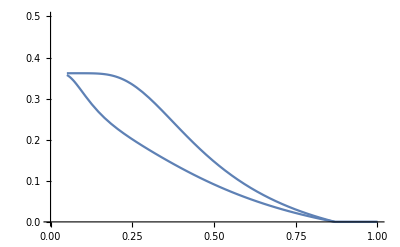

```mathematica
NegativityFNNNfn[x_] := negeal/.β->1/x /.mu->U/2/.U->2 /.t->1
plotFNN=Plot[NegativityFNNNfn[x],{x,0.05,1} , PlotRange->{0,0.5}];
NegativityFNNNfn[x_] := negeal/.β->1/x /.mu->U/100/.U->2 /.t->1
plotFNNN=Plot[NegativityFNNNfn[x],{x,0.05,1} , PlotRange->{0,0.5}];
Show[plotFNN,plotFNNN]
```

# Hubbard Dimer PSSR

## Variables to be set

Set number of fermionic modes, .i.e: number of sites * 2for spins

```mathematica
nsites = 2;
numModes=nsites*2;
```

## Results

```mathematica
Tr[rhoMatrix[1,1,rhoSolution,Tr[rhoSolution]]]//FullSimplify
```

1

```mathematica
Tr[rhoSolution]//FullSimplify
```

1+3 ⅇ^(2 mu β)+2 ⅇ^((mu-t) β)+2 ⅇ^((mu+t) β)+ⅇ^((2 mu-U) β)+2 ⅇ^((3 mu+t-U) β)+2 ⅇ^(-(-3 mu+t+U) β)+ⅇ^(1/2 (4 mu-U+√(16 t^2+U^2)) β)+ⅇ^(-1/2 (-4 mu+U+√(16 t^2+U^2)) β)+ⅇ^(4 mu β-2 U β)

```mathematica
rhotb = Refine[getRhoFTBPSSR[1,2],β>0]//FullSimplify
```

{{ⅇ^(-10 mu β+3 U β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)),(ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β) (U-ⅇ^(√(16 t^2+U^2) β) U-(1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2)),0,0},{(ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β) (U-ⅇ^(√(16 t^2+U^2) β) U-(1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2)))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2)),ⅇ^(-10 mu β+3 U β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)),0,0},{0,0,ⅇ^(3 (-4 mu+U) β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)),(ⅇ^(-1/2 (24 mu-5 U+√(16 t^2+U^2)) β) (-2 ⅇ^(1/2 (4 mu-U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+ⅇ^((2 mu+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 mu β) (U+√(16 t^2+U^2))))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2))},{0,0,(ⅇ^(-1/2 (24 mu-5 U+√(16 t^2+U^2)) β) (-2 ⅇ^(1/2 (4 mu-U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+ⅇ^((2 mu+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 mu β) (U+√(16 t^2+U^2))))/(4 (2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β)) √(16 t^2+U^2)),ⅇ^((-8 mu+U) β)/(2 ⅇ^(-(11 mu+t-3 U) β)+2 ⅇ^(-(9 mu+t-2 U) β)+ⅇ^((-8 mu+U) β)+ⅇ^(2 (-5 mu+U) β)+ⅇ^(3 (-4 mu+U) β)+2 ⅇ^((-9 mu+t+2 U) β)+2 ⅇ^((-11 mu+t+3 U) β)+ⅇ^(-1/2 (20 mu-5 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (-20 mu+5 U+√(16 t^2+U^2)) β)+3 ⅇ^(-10 mu β+3 U β))}}

```mathematica
neg = Negativity[rhotb]
```

1/2 (10+1/8 ⅇ^Re[1] Abs[(4 ⅇ^1 √(16 t^2+U^2)+1+√(1^2-1))/((ⅇ^1+8+ⅇ^1) √1)])
 |  |  |  |

```mathematica
negeal = Refine[neg,{β>0, U >0, t>0, mu>0}]
```

1/2 (9+1+(ⅇ^1 Abs[1])/(8 (ⅇ^1+8+ⅇ^1) √(16 t^2+U^2)))
 |  |  |  |

```mathematica
negeal = negeal//Simplify
```

(ⅇ^(-1/2 (40 mu-2 t-8 U+√(16 t^2+U^2)) β) (-4 ⅇ^((24 mu-4 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-4 ⅇ^((20 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-8 ⅇ^((22 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+Abs[-4 ⅇ^((22 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^((44 mu-5 U+√(16 t^2+U^2)) β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U ((1+ⅇ^(2 √(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)+2 ⅇ^((U+√(16 t^2+U^2)) β)-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β)) U+(-1+ⅇ^(√(16 t^2+U^2) β)) (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))))]+Abs[4 ⅇ^((22 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^((44 mu-5 U+√(16 t^2+U^2)) β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U ((1+ⅇ^(2 √(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)+2 ⅇ^((U+√(16 t^2+U^2)) β)-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β)) U+(-1+ⅇ^(√(16 t^2+U^2) β)) (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β)) √(16 t^2+U^2))))]+Abs[2 ⅇ^((24 mu-4 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 ⅇ^((20 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)-√2 √(ⅇ^((40 mu-5 U+√(16 t^2+U^2)) β) (16 ⅇ^((4 mu+√(16 t^2+U^2)) β) t^2+2 ⅇ^((8 mu-3 U+√(16 t^2+U^2)) β) (16 t^2+U^2)-2 ⅇ^((4 mu-U+√(16 t^2+U^2)) β) (16 t^2+U^2)+2 ⅇ^((U+√(16 t^2+U^2)) β) (16 t^2+U^2)+ⅇ^(2 (2 mu+√(16 t^2+U^2)) β) (8 t^2+U^2-U √(16 t^2+U^2))+2 ⅇ^(1/2 (8 mu-U+3 √(16 t^2+U^2)) β) (-16 t^2+U (-U+√(16 t^2+U^2)))+ⅇ^(4 mu β) (8 t^2+U (U+√(16 t^2+U^2)))-2 ⅇ^(1/2 (8 mu-U+√(16 t^2+U^2)) β) (16 t^2+U (U+√(16 t^2+U^2)))))]+Abs[2 ⅇ^((24 mu-4 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+2 ⅇ^((20 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^((40 mu-5 U+√(16 t^2+U^2)) β) (16 ⅇ^((4 mu+√(16 t^2+U^2)) β) t^2+2 ⅇ^((8 mu-3 U+√(16 t^2+U^2)) β) (16 t^2+U^2)-2 ⅇ^((4 mu-U+√(16 t^2+U^2)) β) (16 t^2+U^2)+2 ⅇ^((U+√(16 t^2+U^2)) β) (16 t^2+U^2)+ⅇ^(2 (2 mu+√(16 t^2+U^2)) β) (8 t^2+U^2-U √(16 t^2+U^2))+2 ⅇ^(1/2 (8 mu-U+3 √(16 t^2+U^2)) β) (-16 t^2+U (-U+√(16 t^2+U^2)))+ⅇ^(4 mu β) (8 t^2+U (U+√(16 t^2+U^2)))-2 ⅇ^(1/2 (8 mu-U+√(16 t^2+U^2)) β) (16 t^2+U (U+√(16 t^2+U^2)))))]))/(8 (ⅇ^(1/2 (8 mu+2 t+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (6 mu+2 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (4 mu+2 t+2 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (6 mu+4 t+2 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (2 mu+4 U+√(16 t^2+U^2)) β)+ⅇ^(1/2 (2 t+4 U+√(16 t^2+U^2)) β)+3 ⅇ^(1/2 (4 mu+2 t+4 U+√(16 t^2+U^2)) β)+2 ⅇ^(1/2 (2 mu+4 t+4 U+√(16 t^2+U^2)) β)+ⅇ^(2 mu β+t β+(3 U β)/2)+ⅇ^(2 mu β+t β+(3 U β)/2+√(16 t^2+U^2) β)) √(16 t^2+U^2))

```mathematica
(*This is the final result for the PSSR*)
```

```mathematica
negeal = negeal//FullSimplify
```

(ⅇ^(-(22 mu-3 U+√(16 t^2+U^2)) β) (Abs[-4 ⅇ^((22 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^((44 mu-5 U+√(16 t^2+U^2)) β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U^2+U (2 ⅇ^((U+√(16 t^2+U^2)) β) U-√(16 t^2+U^2)+2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 √(16 t^2+U^2) β) (U+√(16 t^2+U^2))-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β) (U+√(16 t^2+U^2)))))]+Abs[4 ⅇ^((22 mu-2 U+√(16 t^2+U^2)) β) √(16 t^2+U^2)+√2 √(ⅇ^((44 mu-5 U+√(16 t^2+U^2)) β) (8 (1+ⅇ^(√(16 t^2+U^2) β)-2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β))^2 t^2+U^2+U (2 ⅇ^((U+√(16 t^2+U^2)) β) U-√(16 t^2+U^2)+2 ⅇ^(1/2 (U+√(16 t^2+U^2)) β) (-U+√(16 t^2+U^2))+ⅇ^(2 √(16 t^2+U^2) β) (U+√(16 t^2+U^2))-2 ⅇ^(1/2 (U+3 √(16 t^2+U^2)) β) (U+√(16 t^2+U^2)))))]+Abs[2 ⅇ^((20 mu-4 U+√(16 t^2+U^2)) β) (ⅇ^(4 mu β)+ⅇ^(2 U β)) √(16 t^2+U^2)-√2 √(ⅇ^((40 mu-5 U+√(16 t^2+U^2)) β) (16 ⅇ^((4 mu+√(16 t^2+U^2)) β) t^2+2 ⅇ^((8 mu-3 U+√(16 t^2+U^2)) β) (16 t^2+U^2)-2 ⅇ^((4 mu-U+√(16 t^2+U^2)) β) (16 t^2+U^2)+2 ⅇ^((U+√(16 t^2+U^2)) β) (16 t^2+U^2)+ⅇ^(2 (2 mu+√(16 t^2+U^2)) β) (8 t^2+U^2-U √(16 t^2+U^2))+2 ⅇ^(1/2 (8 mu-U+3 √(16 t^2+U^2)) β) (-16 t^2+U (-U+√(16 t^2+U^2)))+ⅇ^(4 mu β) (8 t^2+U (U+√(16 t^2+U^2)))-2 ⅇ^(1/2 (8 mu-U+√(16 t^2+U^2)) β) (16 t^2+U (U+√(16 t^2+U^2)))))]+Abs[2 ⅇ^((20 mu-4 U+√(16 t^2+U^2)) β) (ⅇ^(4 mu β)+ⅇ^(2 U β)) √(16 t^2+U^2)+√2 √(ⅇ^((40 mu-5 U+√(16 t^2+U^2)) β) (16 ⅇ^((4 mu+√(16 t^2+U^2)) β) t^2+2 ⅇ^((8 mu-3 U+√(16 t^2+U^2)) β) (16 t^2+U^2)-2 ⅇ^((4 mu-U+√(16 t^2+U^2)) β) (16 t^2+U^2)+2 ⅇ^((U+√(16 t^2+U^2)) β) (16 t^2+U^2)+ⅇ^(2 (2 mu+√(16 t^2+U^2)) β) (8 t^2+U^2-U √(16 t^2+U^2))+2 ⅇ^(1/2 (8 mu-U+3 √(16 t^2+U^2)) β) (-16 t^2+U (-U+√(16 t^2+U^2)))+ⅇ^(4 mu β) (8 t^2+U (U+√(16 t^2+U^2)))-2 ⅇ^(1/2 (8 mu-U+√(16 t^2+U^2)) β) (16 t^2+U (U+√(16 t^2+U^2)))))]-8 ⅇ^((22 mu-3 U+√(16 t^2+U^2)) β) √(16 t^2+U^2) (ⅇ^(U β)+Cosh[2 mu β-U β])))/(8 (1+2 ⅇ^((mu-t) β)+2 ⅇ^((mu+t) β)+2 ⅇ^(-(mu+t-U) β)+3 ⅇ^(U β)+ⅇ^((-2 mu+U) β)+2 ⅇ^((-mu+t+U) β)+ⅇ^(1/2 (U-√(16 t^2+U^2)) β)+ⅇ^(1/2 (U+√(16 t^2+U^2)) β)+ⅇ^(2 mu β-U β)) √(16 t^2+U^2))

```mathematica
(*Plot of the NSSR negativity for different parameters*)
```

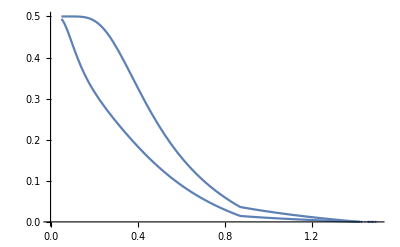

```mathematica
NegativityFNNNfn[x_] := negeal/.β->1/x /.mu->U/2/.U->2 /.t->1
plotFNN=Plot[NegativityFNNNfn[x],{x,0.05,1.5} , PlotRange->{0,0.5}];
NegativityFNNNfn[x_] := negeal/.β->1/x /.mu->U/100/.U->2 /.t->1
plotFNNN=Plot[NegativityFNNNfn[x],{x,0.05,1.5} , PlotRange->{0,0.5}];
Show[plotFNN,plotFNNN]
```